```mathematica
filesAR=FileNames["/home/carla/GDC/MUR/GDC_Conf_AR_MUR_ALL_Out/*.txt"];
dataAR=Map[Get[#]&, filesAR];
filesBR=FileNames["/home/carla/GDC/MUR/GDC_Conf_BR_MUR_ALL_Out/*.txt"];
dataBR=Map[Get[#]&, filesBR];
```

```mathematica
confAR=dataAR[[All,1]];
confBR=dataBR[[All,1]];
```

```mathematica
dojAR=confAR[[All,1]][[All,1]]
zAR=confAR[[All,2]][[All,1]]
fAR=confAR[[All,3]][[All,1]]
```

{0.000584864,0.000584864,0.0555556,0.0555556,0.00326797,0.00236407,0.0833333,1.}

{0.000452197,0.000457117,0.0554259,0.0554295,0.00317624,0.00236113,0.0833214,1.}

{0.630214,0.641469,0.995342,0.995473,0.945392,0.997523,0.999713,1}

```mathematica
dojBR=confBR[[All,1]][[All,1]]
zBR=confBR[[All,2]][[All,1]]
fBR=confBR[[All,3]][[All,1]]
```

{0.000584864,0.00038613,0.0555556,0.0140845,0.00410397,0.00236407,0.25}

{0.000457117,0.00026449,0.0554295,0.0140578,0.00404663,0.00236115,0.24999}

{0.641469,0.520886,0.995473,0.996214,0.972441,0.997533,0.999922}

```mathematica
sList={1,2,3,4,5,6,7,8};
sList2={1.5,2.5,3.5,4.5,5.5,6.5,7.5};
ran=Range[Length[sList]];
ran2=Range[Length[sList2]];


dojPAR={#[[2]],#[[1]]}&/@Map[{dojAR[[#]],sList[[#]]}&,ran];
zPAR= {#[[2]],#[[1]]}&/@Map[{zAR[[#]],sList[[#]]}&,ran];
fPAR= {#[[2]],#[[1]]}&/@Map[{fAR[[#]],sList[[#]]}&, ran];
dojPBR={#[[2]],#[[1]]}&/@Map[{dojBR[[#]],sList2[[#]]}&, ran2];
zPBR= {#[[2]],#[[1]]}&/@Map[{zBR[[#]],sList2[[#]]}&, ran2];
fPBR= {#[[2]],#[[1]]}&/@Map[{fBR[[#]],sList2[[#]]}&, ran2];
```

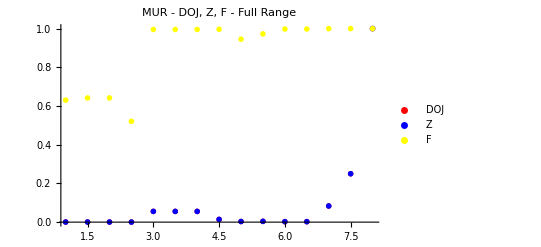

```mathematica
PlotAllParts=ListPlot[{Union[dojPAR,dojPBR], Union[zPAR,zPBR], Union[fPAR, fPBR]}, PlotLegends->{"DOJ","Z", "F"}, PlotStyle-> {Red, Blue, Yellow}, PlotRange->All, PlotLabel->"MUR - DOJ, Z, F - Full Range", PlotMarkers->{{"D",12},{"Z",12},{"F",12}}]
```

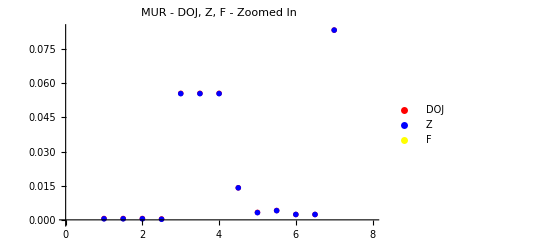

```mathematica
PlotParts=ListPlot[{Union[dojPAR,dojPBR], Union[zPAR,zPBR], Union[fPAR, fPBR]}, PlotLegends->{"DOJ","Z", "F"}, PlotStyle-> {Red, Blue, Yellow}, PlotRange->{-0.001, 0.084},  PlotLabel->"MUR - DOJ, Z, F - Zoomed In",  PlotMarkers->{{"D",12},{"Z",12},{"F",12}}]
```

```mathematica
SetDirectory["/home/carla/GDC/MUR/"];
(*Put[{confM,{bvE,bvHEK}},filenameOut]*)
Put[Union[dojPAR,dojPBR],"MUR_DOJ.txt"]
Put[Union[zPAR,zPBR],"MUR_Z.txt"]
Put[Union[fPAR,fPBR],"MUR_F.txt"]
Export["MUR_ALL.jpeg",PlotAllParts,ImageSize->850]
Export["MUR_Zoomed_In.jpeg",PlotParts,ImageSize->850]
```

MUR_ALL.jpeg

MUR_Zoomed_In.jpeg